```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/c8888/IdeaProjects/ChernRetrieval

```mathematica
δx=0.1;
δy=0.1;
q=2; (* Pi-flux *)
xmin=-5;
xmax=5;
ymin=-5;
ymax=5;
RTF=3;
rangeNeighbour= 0.6;
a=1;
σw=0.2;
k0={1,0}; (* I know that value from experimental setup. I also select the energy band here (let's say its the lowest energy band). I don't know the tunneling amplitude ratio *)
J=1;
J1=2;
nIterations=200;
nRepeats=3;
nHIO=20;
gamma=0.9;
npts=8;(*points in the 1st Brillouin zone*)
```

```mathematica
<<"space.m";
```

```mathematica
?latticeProbingPoints
```

latticeProbingPoints[xmin, xmax, ymin, ymax, δx, δy] generates a list of points {{x_i, y_i}} at which one measures physical variables of BEC in a trap

```mathematica
lat=latticeProbingPoints[xmin,xmax,ymin,ymax,δx,δy];
```

```mathematica
?rectLatticeSites
```

rectLatticeSites[ax, ay, RTF, latticeProbingPoints] generates a list: {{x_i,y_i},type_i} are the rectangular lattice sites, where type_i is the i-th lattice site type (-1 - type A or 1 - type B)

rectLatticeSites[ax, ay, RTF, latticeProbingPoints] generates a list: {{x_i,y_i},type_i} are the rectangular lattice sites, where type_i is the i-th lattice site type (-1 - type A or 1 - type B)\n

```mathematica
rec=rectLatticeSites[a,RTF, xmin, xmax, ymin, ymax];
```

```mathematica
pos=rectLatticeSitesPos[lat,a, δx,δy,RTF];
```

```mathematica
neighpos=rectLatticeSitesNeighbourhood[pos,lat,δx,δy,rangeNeighbour];
```

```mathematica
recA=Map[If[#[[2]]==-1,#[[1]]]&,rec];
```

```mathematica
recB=Map[If[#[[2]]==1,#[[1]]]&,rec];
```

```mathematica
(*p1=ListPlot[lat]*)
```

```mathematica
(*p2A=ListPlot[recA,PlotStyle->{PointSize->0.05,Green},AspectRatio->1]*)
```

```mathematica
(*p2B=ListPlot[recB,PlotStyle->{PointSize->0.05,Red},AspectRatio->1]*)
```

```mathematica
(*pospos={}; (* coordinates of the probing points nearest to the nodes *)*)
```

```mathematica
(*Map[pospos={};AppendTo[pospos,lat[[#[[1]], #[[2]]]]]&, pos];*)
```

```mathematica
(*p4=ListPlot[pospos,PlotStyle->{PointSize->0.015}]*)
```

```mathematica
(*neighpospos={};*)
```

```mathematica
(*Map[neighpospos={};AppendTo[neighpospos,lat[[#[[1]], #[[2]]]]]&, Flatten[neighpos,1]];*)
```

```mathematica
(*p5=ListPlot[neighpospos,PlotStyle->{PointSize->0.03}]*)
```

```mathematica
(*Show[ p2A,p2B,p4,p1,p5,PlotRange->All]*)
```

```mathematica
<<"wavefunction.m";
```

```mathematica
β=wannierNormalisationFactor[σw,δx,δy,lat];
```

```mathematica
(*Plot3D[wannier[{x,y},{0,0},σw,β],{x,-2σw,2σw},{y,-2σw,2σw}]*)
```

```mathematica
wavef=waveFunctionHarper[lat,a,J,J1,rec,RTF,k0,σw,β, δx, δy];
```

```mathematica
(*ListPlot3D[Abs@wavef]*)
```

```mathematica
(*ListDensityPlot[Table[{Flatten[lat,1][[i,1]],Flatten[lat,1][[i,2]],Abs@Flatten[wavef,1][[i]]},{i,Length[Flatten[lat,1]]}], AspectRatio->1,ColorFunction->"Rainbow",AxesLabel->{"x","y","|ψ|"},PlotRange->All]*)
```

```mathematica
FTwavef=Fourier[wavef];
```

```mathematica
(*ListPlot3D[Abs@mirror2DSpace[FTwavef],PlotRange->All,ColorFunction->"Rainbow"]*)
```

```mathematica
FTXAbs=Abs@Fourier[wavef];
```

```mathematica
wavefAbs=Abs@wavef;
```

```mathematica
support=Map[If[Norm[#]<RTF,1,0]&,lat,{2}];
```

```mathematica
<<"HIOER.m"
```

```mathematica
retr=phaseRetrieveSupport[FTXAbs,wavefAbs,support,nIterations,nRepeats,nHIO,gamma];
```

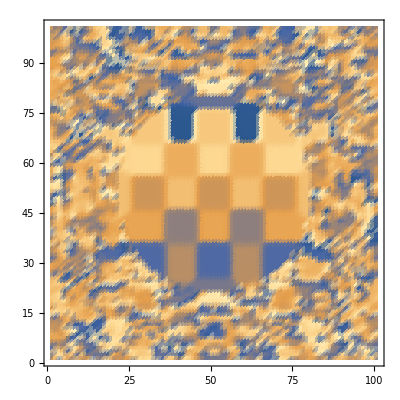

```mathematica
ListDensityPlot[Arg@retr]
```

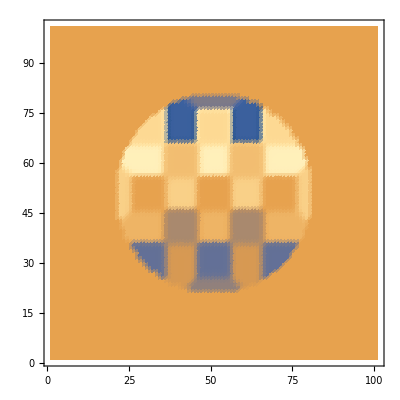

```mathematica
ListDensityPlot[Arg@wavef]
```

```mathematica
rec[[2]]
```

{{-2.,-2.},1.}

```mathematica
ckModel=wannierBaseRectProject[wavef,lat,rec,pos,neighpos,σw,β,δx,δy];
```

```mathematica
ckRetr=wannierBaseRectProject[retr,lat,rec,pos,neighpos,σw,β,δx,δy];
```

```mathematica
Total[Abs[ckRetr]^2]
```

0.985184

```mathematica
Abs[Conjugate[ckRetr].ckModel]^2
```

0.970593

```mathematica
guess[J_,J1_, ckModel_]:=Module[{
wavefJJ1 = waveFunctionHarper[lat,a,J,J1,rec,RTF,k0,σw,β, δx, δy]
},
1-Abs[Conjugate[wannierBaseRectProject[phaseRetrieveSupport[FTXAbs,Abs@wavefJJ1,support,nIterations,nRepeats,nHIO,gamma],lat,rec,pos,neighpos,σw,β,δx,δy]].ckModel]^2
]
```

```mathematica
(*guessT=ParallelTable[{J,J1,guess[J,J1,ckModel]},{J,0.33,2,0.33},{J1,0.33,2,0.33}, DistributedContexts->{"space`","wavefunction`","HIOER`"}]*)
```

```mathematica
(*ListPlot3D[Flatten[guessT,1]]*)
```

```mathematica
guess2[J_,J1_]:=Module[{
wavefJJ1 = waveFunctionHarper[lat,a,J,J1,rec,RTF,k0,σw,β, δx, δy]
},
wavefJJ1=phaseRetrieveSupport[FTXAbs,Abs@wavefJJ1,support,nIterations,nRepeats,nHIO,gamma]; (*nie ma nic wspolnego z wavefJJ1, jest to obiekt odzyskany w tej samej pamieci*)
Total@Total@Abs[Abs[Fourier[wavefJJ1]]^2-Abs[FTXAbs]^2]/Total[Total[Abs[FTXAbs]^2]] (*metryka bledu*)
]
```

```mathematica
guess2T=ParallelTable[{J1,guess2[J,J1]},{J1,0.1,3,0.3}, DistributedContexts->{"space`","wavefunction`","HIOER`"}]
```

{{0.1,0.148085},{0.4,0.15923},{0.7,0.14831},{1.,0.12823},{1.3,0.096442},{1.6,0.0507908},{1.9,0.0122207},{2.2,0.023032},{2.5,0.0616047},{2.8,0.085457}}

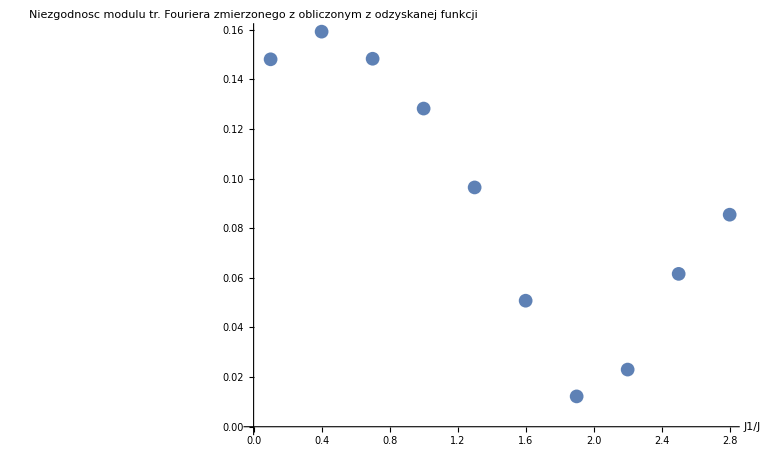

```mathematica
ListPlot[guess2T,AxesLabel->{"J1/J","Niezgodnosc modulu tr. Fouriera zmierzonego z obliczonym z odzyskanej funkcji" } ]
```

```mathematica
(* find ckretr for kx,ky 2d table of 1st BZ*)
(* find Fxy for this set of ckretr*)
(* find chern number *)
```

```mathematica
<<"chernCalc.m"
```

```mathematica
BZ=latticeProbingPointsBZ[npts,a,q];
```

```mathematica
ParallelMap[2*#&,{1,2,3,4,5}]
```

{2,4,6,8,10}

```mathematica
ckRetrBZ=ParallelMap[findCkRetr[#,J,J1,lat,a,rec,RTF,support,nIterations,nRepeats,nHIO,gamma,pos,neighpos,σw,β,δx,δy]&,BZ,{2}];
```

$Aborted

```mathematica
FxyTRetr=FxyT[ckRetrBZ]
```

{{-1.3809×10^-16+0.0687655 ⅈ,3.38271×10^-17+0.355543 ⅈ,-2.21685×10^-17+0.0982131 ⅈ,6.44745×10^-17-0.0978508 ⅈ,7.04935×10^-17+0.134475 ⅈ,-1.06685×10^-16+0.420788 ⅈ,-3.99935×10^-17-0.1645 ⅈ},{0.+1.44863 ⅈ,3.80013×10^-17+0.238288 ⅈ,1.24141×10^-16+0.244944 ⅈ,-5.42643×10^-17-0.245258 ⅈ,-1.11022×10^-16+1.41993 ⅈ,-1.11022×10^-16+1.44367 ⅈ,0.-0.546119 ⅈ},{5.81132×10^-17+0.457157 ⅈ,1.37911×10^-16+0.498764 ⅈ,3.32037×10^-18+0.101025 ⅈ,1.0727×10^-16-0.100219 ⅈ,9.80119×10^-17+0.395473 ⅈ,-1.43115×10^-16+0.460858 ⅈ,-1.01993×10^-16-0.115854 ⅈ},{-4.51028×10^-17+0.515187 ⅈ,1.70003×10^-16+0.516663 ⅈ,-1.44783×10^-16+0.103452 ⅈ,-1.19541×10^-16+0.0501798 ⅈ,6.67869×10^-17-0.402205 ⅈ,-1.11022×10^-16-0.54286 ⅈ,-2.89926×10^-16-0.122203 ⅈ},{0.+1.03538 ⅈ,7.89299×10^-17+0.489158 ⅈ,0.+0.531195 ⅈ,5.01159×10^-17+0.0439704 ⅈ,0.-1.68044 ⅈ,-1.11022×10^-16-1.02857 ⅈ,-2.53812×10^-16-0.258009 ⅈ},{7.57476×10^-17-0.0633746 ⅈ,-6.30464×10^-17-0.224248 ⅈ,4.58618×10^-17+0.240192 ⅈ,1.21415×10^-18-0.0186871 ⅈ,-1.38778×10^-17+0.466736 ⅈ,1.66425×10^-17+0.220924 ⅈ,-2.0042×10^-16-0.00696026 ⅈ},{1.77199×10^-17-0.12218 ⅈ,2.55296×10^-17-0.00543732 ⅈ,2.57047×10^-16+0.0107116 ⅈ,9.84067×10^-18-0.0112124 ⅈ,-3.45081×10^-17-0.11259 ⅈ,2.38256×10^-16-0.0290155 ⅈ,-8.65135×10^-17+0.0379515 ⅈ}}

```mathematica
ckModelBZ=ParallelMap[findCkModel[#,J,J1,lat,a,rec,RTF,support,nIterations,nRepeats,nHIO,gamma,pos,neighpos,σw,β,δx,δy]&,BZ,{2}];
```

```mathematica
FxyTModel=FxyT[ckModelBZ]
```

{{8.21148×10^-17-0.14861 ⅈ,-2.21177×10^-17-0.143572 ⅈ,-4.53036×10^-18-0.0367395 ⅈ,-4.53036×10^-18+0.0367395 ⅈ,1.77809×10^-17+0.143572 ⅈ,-2.68103×10^-16+0.14861 ⅈ,1.04905×10^-16+0.0397157 ⅈ},{-1.59378×10^-17-0.242186 ⅈ,3.46945×10^-18-0.234061 ⅈ,1.45576×10^-16-0.0437793 ⅈ,-8.35202×10^-17+0.0437793 ⅈ,-2.64545×10^-16+0.234061 ⅈ,1.18178×10^-17+0.242186 ⅈ,7.69069×10^-17+0.0469189 ⅈ},{0.-0.52752 ⅈ,-5.55112×10^-17-0.507011 ⅈ,9.15293×10^-17-0.0503007 ⅈ,1.02805×10^-16+0.0503007 ⅈ,-6.93889×10^-17+0.507011 ⅈ,0.+0.52752 ⅈ,-8.45074×10^-17+0.05351 ⅈ},{0.-0.530053 ⅈ,-1.42247×10^-16-0.509787 ⅈ,-9.86753×10^-17-0.0506088 ⅈ,-1.07132×10^-16+0.0506088 ⅈ,-1.14492×10^-16+0.509787 ⅈ,-1.11022×10^-16+0.530053 ⅈ,-7.00517×10^-17+0.053724 ⅈ},{-2.86229×10^-17-0.243116 ⅈ,-5.41559×10^-17-0.235193 ⅈ,2.67851×10^-17-0.0440932 ⅈ,-7.92504×10^-17+0.0440932 ⅈ,1.78893×10^-18+0.235193 ⅈ,-7.80626×10^-18+0.243116 ⅈ,-3.04755×10^-17+0.0471269 ⅈ},{1.09836×10^-16-0.147106 ⅈ,1.69108×10^-16-0.142192 ⅈ,-9.05418×10^-17-0.0364969 ⅈ,-9.66134×10^-17+0.0364969 ⅈ,-5.93668×10^-17+0.142192 ⅈ,1.09836×10^-16+0.147106 ⅈ,-6.1783×10^-17+0.039404 ⅈ},{-1.27699×10^-17-0.118996 ⅈ,1.00438×10^-16-0.114826 ⅈ,1.38551×10^-16-0.0326509 ⅈ,1.40395×10^-16+0.0326509 ⅈ,1.42071×10^-16+0.114826 ⅈ,-1.12601×10^-16+0.118996 ⅈ,-3.97984×10^-17+0.0354833 ⅈ}}

```mathematica
{ListPlot3D[Abs[FxyT[ckRetrBZ]],PlotRange->All],ListPlot3D[Abs[FxyT[ckModelBZ]],PlotRange->All]}
```

{-Graphics3D-,-Graphics3D-}

```mathematica
w=1/(2π ⅈ )*Total@Total[FxyT[ckRetrBZ]]//Chop
```

0.978869

```mathematica
w=1/(2π ⅈ )*Total@Total[FxyT[ckModelBZ]]//Chop
```

0.0502743